# Задание 09.

## Фракталы. Стандартное отображение (Чирикова-Тейлора).

## Мосейков Игнатий Геннадьевич, группа 21372

## Задача

Орбиты

Рассмотрим отображение z_(i+1)=f(z_i),  которое  переводит точку z_i на комплексной плоскости в новое положение z_(i+1). Орбитой (или траекторией) будем называть последовательные положения при применении этого отображения.

Напишите функцию отрисовки орбит, которая принимает функцию-отображение f, начальное положение z_0 и число итерации n_iter и рисует точки соответствующей орбиты (линиями точки орбиты лучше не соединять, а использовать, например, конструкцию

Graphics[{Red, PointSize[0.02], Point[{x0, y0}], Point[{x1, y1}], ...}]).

1) Нарисуйте орбиту для f(z)=z^2+c, c=(0.33+0.35ⅈ), z_0=0.25 (на вещественной оси).

2) Что происходит с орбитой начинающейся в точке z_0=2  для отображения из предыдущего пункта?

3) Рассмотрите другую функцию-отображение f'(z)=(λ+α(|z|)^2+β Re(z^n))z+γ (z^*)^(n-1), здесь |z| — модуль комплексного числа, Re — взятие реальной части, z^* — комплексное сопряжение. Попробуйте разные значения параметров и нарисуйте орбиты (точек на орбите может потребоваться достаточно много (~10^4 или 10^5); и нарисовать их нужно достаточно мелкими, чтобы увидеть детали):

λ = 1.52,   α = -1,   β = 0.1,   γ = -0.8,   n = 3,   z_0= 0.1-0.1 ⅈ

λ = -2.585,   α = 5,   β = 2,   γ = 1,   n = 6,   z_0= 0.2-0.1 ⅈ

λ = -2.6,   α = 4,   β = 2,   γ = 1,   n = 8,   z_0= -0.2 + 0.1ⅈ

λ = -1.75,   α =2,   β = -0.2,   γ = 1,   n = 3,   z_0= 0.2 + 0.1 ⅈ

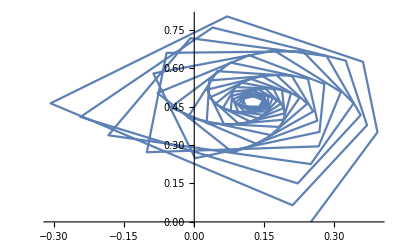

```mathematica
f[z_]:=z*z+0.33+0.35I;
Orbit[func_,z0_,niter_]:=Block[{trajectory,list},trajectory=NestList[func,z0,niter];list=Table[{trajectory[[i]]//Re,trajectory[[i]]//Im},{i,1,niter}]];
ListPlot[Orbit[f,0.25,100],Joined->True]
```

```mathematica
ListPlot[Orbit[f,2,10],Joined->True]
```

-Graphics-

```mathematica
CreateFwithParams[Fname_,lambda_,alpha_,beta_,gamma_,n_]:=Fname[z_]:=(lambda+alpha*z*Conjugate[z]+beta*Re[Power[z,n]])*z+gamma*Power[z//Conjugate,n-1];
```

```mathematica
Clear[F];
CreateFwithParams[F,1.52,-1,0.1,-0.8,3];
```

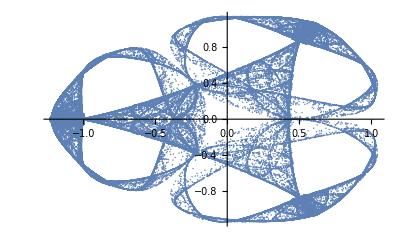

```mathematica
ListPlot[Orbit[F,0.1-0.1I,100000],PlotStyle->AbsolutePointSize[1]]
```

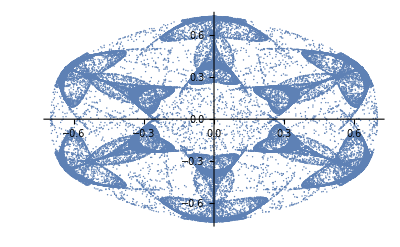

```mathematica
Clear[F];
CreateFwithParams[F,-2.585,5,2,1,6];
ListPlot[Orbit[F,0.2-0.1I,100000],PlotStyle->AbsolutePointSize[1]]
```

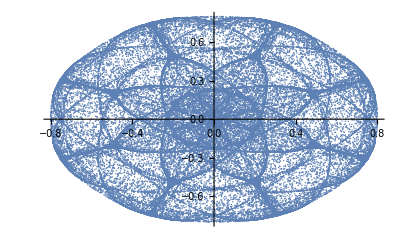

```mathematica
Clear[F];
CreateFwithParams[F,-2.6,4,2,1,8];
ListPlot[Orbit[F,-0.2+0.1I,100000],PlotStyle->AbsolutePointSize[1]]
```

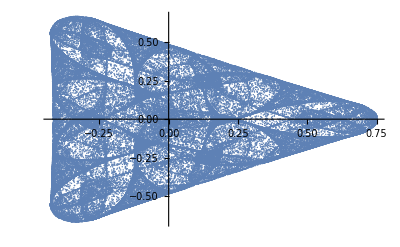

```mathematica
Clear[F];
CreateFwithParams[F,-1.75,2,-0.2,1,3];
ListPlot[Orbit[F,0.2+0.1I,100000],PlotStyle->AbsolutePointSize[1]]
```

Множество Мандельброта

Возвращаемся к отображению z_(i+1)=z_i^2+c, где c —  комплексное число, и z_0=0. Если орбита не  уходит на бесконечность, то точка c принадлежит множеству Мандельброта.

1) Напишите функцию, которая для каждого значения проверяет, убегает ли орбита на бесконечность. Конечно, нельзя реализовать бесконечный процесс, чтобы проверять это. Но можно показать, что если расстояние от текущего положения точки до начала координат уже оказалость больше 2, то оно будет продолжать неограничено увеличиваться. Как результат: если модуль |z_i| не превышает 2 за, скажем, n_iter=100 итераций (число итераций можно менять), то условно можно говорить, что c принадлежит множеству Мандельброта. А если z_n в какой-то  момент уходит на бо^`льшие расстояния, можно прекращать итерации — данное значение c не принадлежит множеству Мандельброта.

2) Нарисуйте на комплексной плоскости точки, принадлежащие множеству Мандельброта (чтобы не уйти сразу в очень долгие вычисления, можно проверять значения на сетке, постепенно уменьшая шаг). Покрасьте точки, которые не принадлежат множеству Мандельброта, цветом  отображая число итераций, после которых |z_i| становится больше 2

```mathematica
MandelbrotChecker[c_,niter_]:=Block[{i=0,z=0},f[z_]:=z*z+c;While[i<niter&&z*Conjugate[z]<4,z=f[z];i++];If[i==niter,True,False]];
MandelbrotChecker[0.,200]
```

True

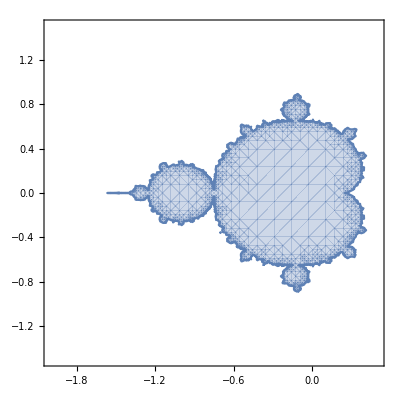

```mathematica
RegionPlot[MandelbrotChecker[x+I*y,100]==True,{x,-2.0,0.5},{y,-1.5,1.5},MaxRecursion->5]
```

```mathematica
MandelbrotNIterations[c_,niter_]:=Block[{i=0,z=0},f[z_]:=z*z+c;While[i<niter&&z*Conjugate[z]<4,z=f[z];i++];i];
DensityPlot[MandelbrotNIterations[x+I*y,100],{x,-2.0,0.5},{y,-1.5,1.5},MaxRecursion->5 ,ColorFunction->GrayLevel]
```

-Graphics-

Множество Жюлиа

При построении множества Мандельброта фиксировалось z_0. Теперь мы зафиксируем значение c и будем менять z_0. Если орбита не  уходит на бесконечность, то точка z_0 принадлежит множеству Жюлиа.

1) Получите цветной рисунок для множества Жюлиа для c=-1 (аналогично пункту 2 из предыдущего задания)

```mathematica
JuliaNIterations[z0_,niter_]:=Block[{i=0,z=z0},f[z_]:=z*z-1;While[i<niter&&z*Conjugate[z]<4,z=f[z];i++];i];
DensityPlot[JuliaNIterations[x+I*y,100],{x,-2.0,2.0},{y,-1.0,1.0},MaxRecursion->5 ,ColorFunction->GrayLevel,AspectRatio->1/2]
```

-Graphics-

Стандартное отображение (Чирикова-Тейлора)

Стандартное отображение — это отображение квадрата (0,1)×(0,1) на себя, которое задается формулами (здесь x, y — вещественные (не комплексные); mod 1 — взятие по модулю 1, функция Mod[]):

x_(i+1)=(x_i+y_i-K/(2π)sin(2π x_i))mod 1
y_(i+1)=(y_i-K/(2π)sin(2π x_i))mod 1

в зависимости от параметра отображения, K, и начального положения {x_0,y_0} снова формируются различные траектории. Ваша задача исследовать поведение этих тректорий в зависимости от параметра 0≤K≤3, и обнаружить качественный переход в этом поведении.

Чтобы сравнить поведение при разных K удобно фиксировать несколько начальных положений (например, на диагонали квадрата с некоторым шагом: {{0, 0}, {0.1, 0.1}, ..., {1., 1.}}) и для каждого начального положения своим цветом нарисовать траекторию длиной ~ 1000 шагов (можно варьировать, начиная с меньших значений, чтобы время расчета оставалось приемлемым)

```mathematica
f[K_]:=xy↦{Mod[xy[[1]]+xy[[2]]-K/(2π)Sin[2π xy[[1]]],1],Mod[xy[[2]]-K/(2π)Sin[2π xy[[1]]],1]};
orbit[K_,xy0_,n_]:=NestList[f[K],xy0,n];
Animate[ListPlot[Table[orbit[K,{i,i},100],{i,0,1,0.05}],PlotLabel->K],{K,0,3,0.05},AnimationRate->0.1]
```